```mathematica
ClearAll["Global`*"]
```

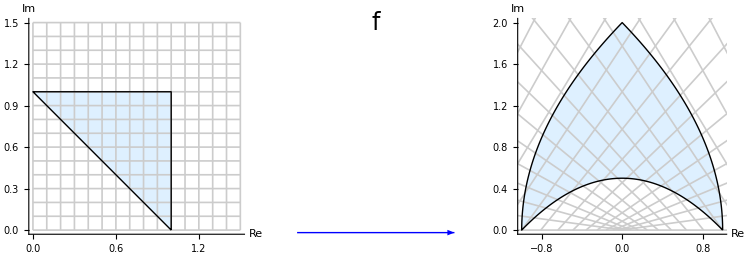

```mathematica
(*Define the complex function*)f[z_]:=z^2

(*Parametrize each side of the triangle*)
side1[t_]:=(1-t)+t I;        (*from 1 to i*)
side2[t_]:=(1-t) I+t (1+I); (*from i to 1+i*)
side3[t_]:=(1-t) (1+I)+t;   (*from 1+i to 1*)

(*Generate dense points along each side for accurate boundary transformation*)
denseSide1=Table[ReIm[side1[t]],{t,0,1,0.01}];
denseSide2=Table[ReIm[side2[t]],{t,0,1,0.01}];
denseSide3=Table[ReIm[side3[t]],{t,0,1,0.01}];
allTrianglePoints=Join[denseSide1,denseSide2,denseSide3];

(*Transform these points*)
transformedPoints1=ReIm[f/@(denseSide1[[All,1]]+I denseSide1[[All,2]])];
transformedPoints2=ReIm[f/@(denseSide2[[All,1]]+I denseSide2[[All,2]])];
transformedPoints3=ReIm[f/@(denseSide3[[All,1]]+I denseSide3[[All,2]])];
allTransformedPoints=Join[transformedPoints1,transformedPoints2,transformedPoints3];

(*Create grid lines parallel to the axes within the bounding box of the triangle*)
gridLinesX=Table[{{x,0},{x,1.5}},{x,0,1.5,0.1}];
gridLinesY=Table[{{0,y},{1.5,y}},{y,0,1.5,0.1}];

(*Transform grid lines*)
transformedGridLinesX=Table[{ReIm[f[Complex@@gridLinesX[[i,1]]]],ReIm[f[Complex@@gridLinesX[[i,2]]]]},{i,1,Length[gridLinesX]}];
transformedGridLinesY=Table[{ReIm[f[Complex@@gridLinesY[[i,1]]]],ReIm[f[Complex@@gridLinesY[[i,2]]]]},{i,1,Length[gridLinesY]}];

(*Grid line thickness setting*)
gridLineThickness=Thickness[0.003];  (*You can change this to Thick,Thin,or {Thickness[x]} where x is a number*)

(*Plot the original and transformed regions with grid lines and filled polygons*)
originalRegion=Graphics[{LightBlue,Polygon[allTrianglePoints],GrayLevel[0.8],gridLineThickness,Line/@gridLinesX,Line/@gridLinesY,Black,Thick,Line[allTrianglePoints]},Axes->True,PlotRange->{{0,1.5},{0,1.5}},AxesLabel->{"Re","Im"}];

transformedRegion=Graphics[{LightBlue,Polygon[allTransformedPoints],GrayLevel[0.8],gridLineThickness,Line/@transformedGridLinesX,Line/@transformedGridLinesY,Black,Thick,Line[allTransformedPoints]},Axes->True,PlotRange->{{-1,1},{0,2}},AxesLabel->{"Re","Im"}];

(*Define an arrow graphic with the label'f'*)arrowGraphic=Graphics[{Blue,Arrowheads[0.05],Arrow[{{0,0},{0.1,0}}],Black,Text[Style["f",FontSize->24],{0.05,0.025}]},ImageSize->Small];

(*Combine the original region,arrow graphic,and transformed region in a row*)
fullGraphic=GraphicsRow[{originalRegion,arrowGraphic,transformedRegion},Spacings->{Scaled[0.1],Scaled[-0.2]},ImagePadding->{{Automatic,Automatic},{10,10}}]
```